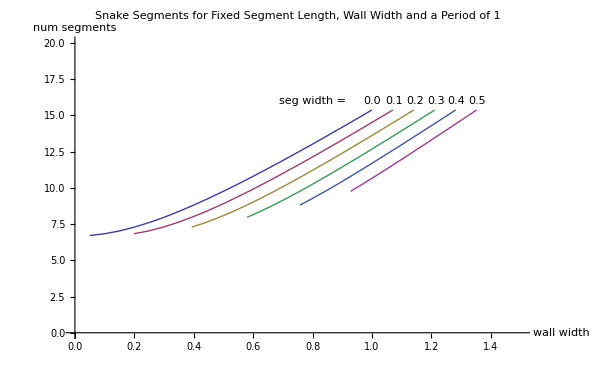

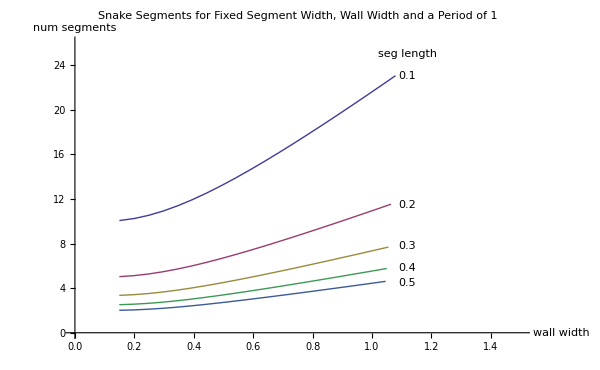

```mathematica
(*
P = 1;
A = 1;
l = 0.15;
w = 0.1;
*)

(* lower limit of distance from curve to the wall with a given robot configuration of l, w, and curve paramters of A and P *)

getLimits[P_,A_,segLen_,segWidth_]:=Module[{expr1, expr2, subs1, subs2, sol, xrule1, xrule2, xval1, xval2, yrule1, yrule2, yval1, yval2, angle, Y, X, K, L},
Off[Reduce::ratnz];
Off[Reduce::incs];
expr1 = segLen^2 == (X-P/2)^2 + (Y+A/2)^2;expr2 = Y == A/2 * Cos[2*Pi*X/P];
subs1  = Solve[expr1, {Y}];
subs2  = Solve[expr2, {Y}]; sol =Reduce[expr1 && expr2  && X > 0 && X < P, {X,Y}, Reals];xrule1=Solve[sol[[1]][[1]],X];
xrule2=Solve[sol[[2]][[1]],X];
xval1 =(X /. xrule1) [[1]];
xval2 =(X/. xrule2 )[[1]] ;yrule1 =Solve[sol[[1]][[2]] /. xrule1[[1]],Y];yrule2 =Solve[sol[[2]][[2]] /. xrule2[[1]],Y];yval1 =(Y /. yrule1) [[1]];
yval2 =(Y /. yrule2 )[[1]] ;
angle = ArcSin[(yval1+A/2)/segLen];
K = segWidth/2 * Cos[angle];
L = getLengthAnchor[P,A,0];
{A+2*K, L/segLen}
]


getLength[P_,W_] := Module[{L}, 2*(P^2/4 + W^2)^(1/2)]

getLengthAnchor[P_, W_, segWidth_] := Module[{x},
Integrate[(((-(W-segWidth)Pi/P )*Sin[2Pi*x/P])^2+1)^(1/2),{ x, 0, P}]
]

(*  Vary the segment length
expr = Hold[getLimits[P, A, segLen,segWidth]]

results = Table[ expr /. {P->1, segLen->sl, segWidth->0.1, A->av}, {sl,0.1,0.5,0.1}, {av, 0.05, 1, 0.05}]

results2 = ReleaseHold[results]
*)


(*  Vary the segment width
expr = Hold[getLimits[P, A, segLen,segWidth]]

results = Table[ expr /. {P->1, segLen->0.15, segWidth->sw, A->av}, {sw,0,0.5,0.1}, {av, If[sw  > 0,sw,0.05], 1, 0.05}]

results2 = ReleaseHold[results]
*)

(* results for varying the segment width with holding segLength = 0.5, P = 1, and varying A and segWidth *)
segWidthResults = {{{0.05,6.707601696168874},{0.1,6.828234857094546},{0.15000000000000002,7.022640174460916},{0.2,7.282556982207851},{0.25,7.598924429129488},{0.30000000000000004,7.9630153399495835},{0.35000000000000003,8.367046971355494},{0.4,8.804388177954143},{0.45,9.269532997111197},{0.5,9.757969816090242},{0.55,10.266021255066107},{0.6000000000000001,10.790690851157681},{0.65,11.329530315825911},{0.7000000000000001,11.8805301732025},{0.75,12.442031945337964},{0.8,13.012658533818733},{0.8500000000000001,13.591259318740313},{0.9,14.176866898043489},{0.9500000000000001,14.768662931783885},{1.,15.365951075691278}},{{0.19908343264959882,6.828234857094546},{0.24800871168246508,7.022640174460916},{0.2966191357265223,7.282556982207851},{0.34499868989601734,7.598924429129488},{0.39322576155148836,7.9630153399495835},{0.44136641731064985,8.367046971355494},{0.48947231952416576,8.804388177954143},{0.5375815597396912,9.269532997111197},{0.5857208280650796,9.757969816090242},{0.6339078891602995,10.266021255066107},{0.6821538435613242,10.790690851157681},{0.730464983456306,11.329530315825911},{0.7788442251715318,11.8805301732025},{0.8272921734189438,12.442031945337964},{0.8758078921236825,13.012658533818733},{0.9243894527332068,13.591259318740313},{0.9730343187719297,14.176866898043489},{1.021739612165933,14.768662931783885},{1.0705022952779355,15.365951075691278}},{{0.3932382714530446,7.282556982207851},{0.43999737979203474,7.598924429129488},{0.4864515231029766,7.9630153399495835},{0.5327328346212997,8.367046971355494},{0.5789446390483315,8.804388177954143},{0.6251631194793825,9.269532997111197},{0.6714416561301592,9.757969816090242},{0.7178157783205991,10.266021255066107},{0.7643076871226484,10.790690851157681},{0.8109299669126118,11.329530315825911},{0.8576884503430635,11.8805301732025},{0.9045843468378876,12.442031945337964},{0.9516157842473648,13.012658533818733},{0.9987789054664137,13.591259318740313},{1.0460686375438595,14.176866898043489},{1.093479224331866,14.768662931783885},{1.141004590555871,15.365951075691278}},{{0.5796772846544649,7.9630153399495835},{0.6240992519319495,8.367046971355494},{0.6684169585724973,8.804388177954143},{0.7127446792190737,9.269532997111197},{0.7571624841952388,9.757969816090242},{0.8017236674808985,10.266021255066107},{0.8464615306839727,10.790690851157681},{0.8913949503689177,11.329530315825911},{0.9365326755145953,11.8805301732025},{0.9818765202568315,12.442031945337966},{1.0274236763710471,13.012658533818733},{1.0731683581996205,13.591259318740313},{1.119102956315789,14.176866898043489},{1.1652188364977991,14.768662931783885},{1.2115068858338067,15.365951075691278}},{{0.757889278096663,8.804388177954143},{0.8003262389587649,9.269532997111197},{0.8428833122603183,9.757969816090242},{0.8856315566411981,10.266021255066107},{0.9286153742452967,10.790690851157681},{0.9718599338252235,11.329530315825911},{1.015376900686127,11.8805301732025},{1.0591686936757752,12.442031945337964},{1.1032315684947296,13.012658533818733},{1.1475578109328273,13.591259318740313},{1.1921372750877188,14.176866898043489},{1.2369584486637322,14.768662931783885},{1.2820091811117422,15.365951075691278}},{{0.928604140325398,9.757969816090242},{0.9695394458014974,10.266021255066107},{1.0107692178066208,10.790690851157681},{1.0523249172815294,11.329530315825911},{1.0942211258576588,11.8805301732025},{1.136460867094719,12.442031945337964},{1.1790394606184118,13.012658533818733},{1.2219472636660336,13.59125931874031},{1.2651715938596484,14.176866898043489},{1.3086980608296652,14.768662931783885},{1.3525114763896777,15.365951075691278}}};

segLengthResults = {{{0.1498864524552201,10.06140254425331},{0.19955092927932055,10.242352285641818},{0.249008046946067,10.533960261691373},{0.2982799118039797,10.923835473311776},{0.3473933980410338,11.39838664369423},{0.3963773499321008,11.944523009924374},{0.4452602080254362,12.550570457033242},{0.49406831240563964,13.206582266931214},{0.5428249089178249,13.904299495666795},{0.591549742208271,14.636954724135363},{0.6402590661330464,15.39903188259916},{0.688965908972702,16.18603627673652},{0.7376804657617055,16.994295473738866},{0.7864105303810757,17.82079525980375},{0.8351619145765125,18.663047918006946},{0.8839388262851077,19.518987800728098},{0.9327441961459072,20.38688897811047},{0.9815799508414275,21.26530034706523},{1.0304472370849485,22.152994397675826},{1.0793466023431713,23.048926613536914}},{{0.14963104765119167,5.030701272126655},{0.1985703874939599,5.121176142820909},{0.2469398409842239,5.2669801308456865},{0.2948978405089992,5.461917736655888},{0.3426006282843734,5.699193321847115},{0.39017837706492575,5.972261504962187},{0.43772747573442694,6.275285228516621},{0.4853130578872376,6.603291133465607},{0.5329756145936545,6.952149747833397},{0.5807379551616059,7.318477362067681},{0.6286109719584794,7.69951594129958},{0.6765979005992583,8.09301813836826},{0.724697271651886,8.497147736869433},{0.7729048746221627,8.910397629901874},{0.8212150279437047,9.331523959003473},{0.8696213807918013,9.759493900364049},{0.9181174068219013,10.193444489055235},{0.966696698538575,10.632650173532616},{1.0153531343132907,11.076497198837913},{1.0640809650745875,11.524463306768457}},{{0.14941284895779738,3.3538008480844366},{0.19774052740230164,3.4141174285472724},{0.2452179924437616,3.5113200872304575},{0.2921467556268236,3.641278491103925},{0.3388117079367588,3.7994622145647434},{0.3854309583815134,3.9815076699747913},{0.4321454931352312,4.183523485677747},{0.47903280926753067,4.402194088977072},{0.5261269673108177,4.634766498555598},{0.5734357538634007,4.878984908045121},{0.6209525923473886,5.133010627533054},{0.6686639235616714,5.39534542557884},{0.7165534560493315,5.664765157912956},{0.7646044707814618,5.940265086601249},{0.81280098684345,6.221015972668981},{0.8611282868240278,6.506329266909366},{0.9095730949125886,6.795629659370156},{0.958123574714815,7.0884334490217435},{1.0067692399059656,7.3843314658919414},{1.0555008285263716,7.682975537845638}},{{0.14936549705858782,2.5153506360633275},{0.19751937620845247,2.5605880714104545},{0.24463945429673373,2.6334900654228433},{0.29101729704119084,2.730958868327944},{0.3370025044704094,2.8495966609235577},{0.38291287196926227,2.9861307524810936},{0.42897102860257325,3.1376426142583105},{0.4752970488188084,3.3016455667328035},{0.5219354210999013,3.4760748739166987},{0.5688865381717727,3.6592386810338406},{0.616129485256934,3.84975797064979},{0.6636353366568126,4.04650906918413},{0.711373945252272,4.2485738684347165},{0.7593170144456453,4.455198814950937},{0.8074392465231234,4.665761979501736},{0.8557185666065621,4.8797469501820245},{0.9041359393885114,5.0967222445276175},{0.9526750336746814,5.316325086766308},{1.0013218545686073,5.5382485994189565},{1.0500643956484388,5.762231653384228}},{{0.14949880599965598,2.012280508850662},{0.19798368147280973,2.0484704571283636},{0.24544206321222833,2.1067920523382746},{0.291928023559819,2.184767094662355},{0.3376492305312777,2.2796773287388463},{0.3829766595161507,2.388904601984875},{0.42831288191821903,2.510114091406648},{0.47393988437695234,2.641316453386243},{0.5199830255776268,2.780859899133359},{0.5664607082145604,2.9273909448270725},{0.6133405912730672,3.0798063765198322},{0.66057372719314,3.237207255347304},{0.7081103359356817,3.3988590947477735},{0.7559056968271481,3.5641590519607496},{0.8039216185567525,3.732609583601389},{0.8521261741580247,3.9037975601456196},{0.9004928764196181,4.077377795622094},{0.9489997673077883,4.2530600694130465},{0.9976285918368137,4.430598879535165},{1.0463641024612158,4.609785322707383}}};

graphResult = ListLinePlot[segWidthResults,PlotLabel->Style["Snake Segments for Fixed Segment Length, Wall Width and a Period of 1",20], AxesLabel->{Style["wall width",15],Style["num segments",15]},
PlotRange->{{0,1.5},{0,20}},
ImageSize->600,
Epilog->{Style[Text["seg width = ",{.8,16}],15],Style[Text["0.0",{1.0,16}],12],
Style[Text["0.1",{1.075,16}],12],
Style[Text["0.2",{1.145,16}],12],
Style[Text["0.3",{1.215,16}],12],
Style[Text["0.4",{1.285,16}],12],
Style[Text["0.5",{1.355,16}],12]

}]
graphResult = ListLinePlot[segLengthResults,PlotLabel->Style["Snake Segments for Fixed Segment Width, Wall Width and a Period of 1",20], AxesLabel->{Style["wall width",15],Style["num segments",15]},
PlotRange->{{0,1.5},{0,26}},
ImageSize->600,
Epilog->{Style[Text["seg length",{1.12,25}],15],
Style[Text["0.1",{1.12,23}],12],
Style[Text["0.2",{1.12,11.5}],12],
Style[Text["0.3",{1.12,7.8}],12],
Style[Text["0.4",{1.12,5.8}],12],
Style[Text["0.5",{1.12,4.5}],12]

}]
```